质数线段图, 质数分布的一个平衡性质

2010-01-29

Suppose p[i] is the i-th prime. Start from coordinate origin (0,0) , first line to (2,0), then line to (2,3), then to (2+5,3), then to (7,3+7), then to (7+11,10), and so go on...... here 2,3,5,7,11 is the prime list. I call this Prime Segment Diagram. It is very interest!

Conjecture: The line y=x intersect with every segment of  Prime Segment Diagram.

It implies the balance of prime distribution.

{376,415}

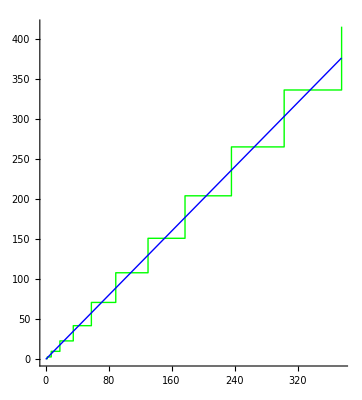

```mathematica
point[0]={0,0};
point[n_]:=If[OddQ[n],{point[n-1][[1]]+Prime[n],point[n-1][[2]]},{point[n-1][[1]],point[n-1][[2]]+Prime[n]}]
n=22;
point[n]
Graphics[{Green,Line[Table[point[i],{i,1,n}]],Blue,Line[{{0,0},{point[n][[1]],point[n][[1]]}}]},Axes->True]
```